# Local order analysis

## 1. Import images of colloid centers

```mathematica
imageDir=NotebookDirectory[]<>"input_files/";
imageCenteredRectangular=Import[imageDir<>"DF_centered_rectangular_20x20.png"];
imageHexagonal=Import[imageDir<>"DF_hexagonal_20x20.png"];
imageOblique=Import[imageDir<>"DF_oblique_20x20.png"];
imageRectangular=Import[imageDir<>"DF_rectangular_20x20.png"];
imageSquare=Import[imageDir<>"DF_square_20x20.png"];
```

## 2. Voronoi Analysis

```mathematica
voronoiAnalysis[imIn_,lengthCutoff_]:=Block[{imData,dims,data,vm,pts,vmVerts,vmFaces,buffer,facesRed,reg,numNeigh,neighColorTable,areaTable,areaMM,areaColors,edgeTable,edgeLengthsTable,edgeLengthsThreshTable,meanAreaPerParticle,massCenters,gyrationTensor,eigenvalueTable,eigenvectorTable,aspectratioTable,aspectratioMin,aspectratioColors,evDirection,evColors,reducedRegion,ptsReduced},

buffer=.1;

imData=ImageData[imIn];
dims =Dimensions[imData][[;;2]];

data = Flatten[Table[{i,j,Mean@imData[[i,j]]},{i,dims[[1]]},{j,dims[[2]]}],1];

pts=Select[data,#[[3]]!=1&][[;;,;;2]];

meanAreaPerParticle=dims[[1]]*dims[[2]]/Length[pts];

vm=VoronoiMesh[pts];
vmVerts=MeshCoordinates[vm];
vmFaces=MeshCells[vm,2][[;;,1]];

reg=Rectangle[buffer*dims,(1-buffer)*dims];

facesRed=Select[vmFaces,RegionMember[reg,Mean/@Transpose[Table[vmVerts[[#[[i]]]],{i,Length@#}]]]&];

reducedRegion=MeshRegion[vmVerts,Polygon/@facesRed];
ptsReduced=Select[pts,RegionMember[reducedRegion,#]&];

edgeTable=Table[Table[{#[[j]],#[[Mod[j,Length@#]+1]]},{j,1,Length@#}]&@facesRed[[i]],{i,Length@facesRed}];
edgeLengthsTable = Table[Table[Norm[(#[[2]]-#[[1]])]&@vmVerts[[edgeTable[[i,j]]]],{j,1,Length@edgeTable[[i]]}],{i,1,Length@edgeTable}];
edgeLengthsThreshTable=Table[{Select[edgeLengthsTable[[i]],#>=lengthCutoff*Total[edgeLengthsTable[[i]]]&],Select[edgeLengthsTable[[i]],#<lengthCutoff*Total[edgeLengthsTable[[i]]]&]},{i,1,Length@edgeTable}];

numNeigh=Table[Length@edgeLengthsThreshTable[[i,1]],{i,1,Length@edgeTable}];
neighColorTable=ColorData[3][#-2]&/@numNeigh;

areaTable=Table[Area@Polygon[vmVerts[[facesRed[[i]]]]],{i,Length@facesRed}];
areaMM=MinMax@areaTable;
areaColors=ColorData["ThermometerColors"][.5+.5(#-meanAreaPerParticle)/meanAreaPerParticle]&/@areaTable;


massCenters=Table[Mean/@Transpose[Table[vmVerts[[facesRed[[i,j]]]],{j,Length@facesRed[[i]]}]],{i,1,Length@facesRed}];
gyrationTensor=Table[Mean@Table[Outer[Times,vmVerts[[facesRed[[i,j]]]]-massCenters[[i]],vmVerts[[facesRed[[i,j]]]]-massCenters[[i]]],{j,Length@facesRed[[i]]}],{i,1,Length@facesRed}];
eigenvalueTable=Eigenvalues/@gyrationTensor;
eigenvectorTable=Eigenvectors/@gyrationTensor;
aspectratioTable=(#[[2]])/(#[[1]])&/@eigenvalueTable;
aspectratioMin=Min@aspectratioTable;
aspectratioColors=ColorData["DeepSeaColors"][#]&/@aspectratioTable;

evDirection=ArcTan[Abs@Tan[ArcTan[#[[1]],#[[2]]]]]&/@eigenvectorTable[[;;,1]];
evColors=Hue[#/π]&/@evDirection;

{
Show[

MeshRegion[vmVerts,Polygon/@facesRed,MeshCellStyle->Join[{{1}->Black},Table[{2,i}->neighColorTable[[i]],{i,1,Length@neighColorTable}]]],
ListPlot[ptsReduced,PlotStyle->Directive[Black]],
PlotRange->All,
ImageSize->500
],

Show[
MeshRegion[vmVerts,Polygon/@facesRed,MeshCellStyle->Join[{{1}->Black},Table[{2,i}->areaColors[[i]],{i,1,Length@areaColors}]]],
ListPlot[ptsReduced,PlotStyle->Directive[Black]],
PlotRange->All,
ImageSize->500
],

(* Plot local measures of anisotropy using eigenvectors of gyration tensor *)
Show[
Graphics[{Black,Table[Point[massCenters[[i]]],{i,1,Length@massCenters}]}],
Graphics[{Table[{evColors[[i]],Polygon[{
massCenters[[i]]-20(1-aspectratioTable[[i]])eigenvectorTable[[i,1]]-20(1-aspectratioTable[[i]])*aspectratioTable[[i]]*eigenvectorTable[[i,2]],
massCenters[[i]]-20(1-aspectratioTable[[i]])eigenvectorTable[[i,1]]+20(1-aspectratioTable[[i]])*aspectratioTable[[i]]*eigenvectorTable[[i,2]],
massCenters[[i]]+20(1-aspectratioTable[[i]])eigenvectorTable[[i,1]]+20(1-aspectratioTable[[i]])*aspectratioTable[[i]]*eigenvectorTable[[i,2]],
massCenters[[i]]+20(1-aspectratioTable[[i]])eigenvectorTable[[i,1]]-20(1-aspectratioTable[[i]])*aspectratioTable[[i]]*eigenvectorTable[[i,2]]}]},{i,1,Length@massCenters}]}],

PlotRange->All,
ImageSize->500
]


}
]
```

```mathematica
voronoiPlotsCenteredRectangular=voronoiAnalysis[imageCenteredRectangular,0];
voronoiPlotsHexagonal=voronoiAnalysis[imageHexagonal,0];
voronoiPlotsOblique=voronoiAnalysis[imageOblique,0.05];
voronoiPlotsRectangular=voronoiAnalysis[imageRectangular,0.05];
voronoiPlotsSquare=voronoiAnalysis[imageSquare,0.05];
```

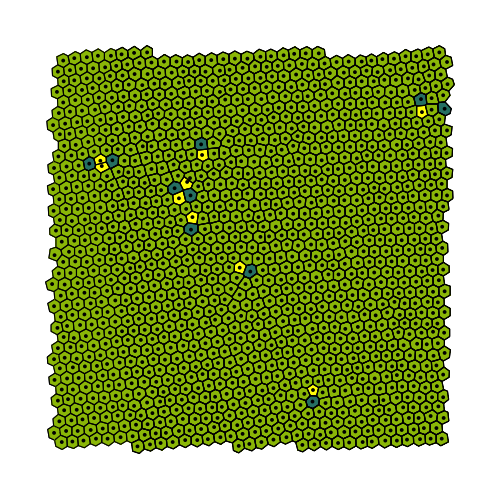
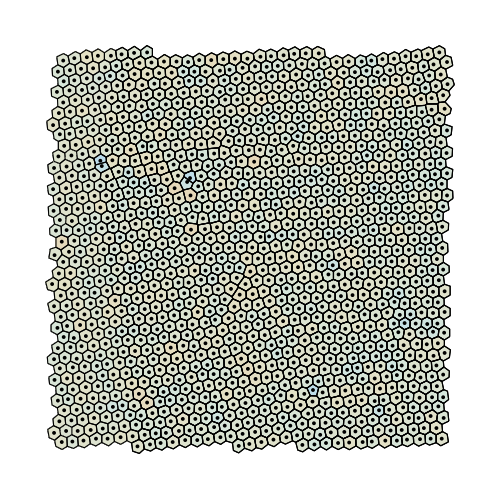
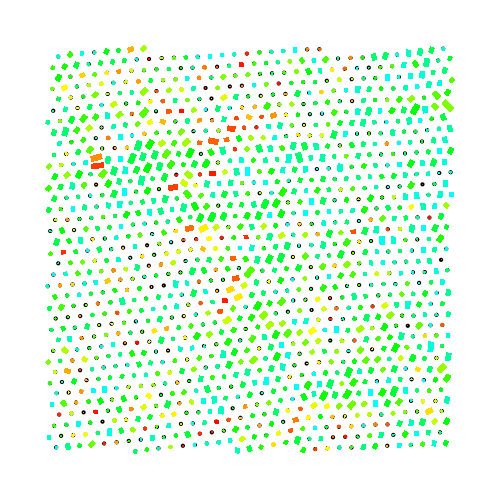

```mathematica
voronoiPlotsHexagonal
```

## 3. Contact Analysis

```mathematica
contactAnalysis[imIn_,diameterMult_]:=Block[{imData,dims,data,dm,ptsData,pts,dmVerts,dmFaces,dmEdges,buffer,reg,diameter,regionSize,edgesRed1,edgesRed2,vm,facesRed,vmVerts,vmFaces,edgeLength,edgeLengthColor,edgeLengthAll,edgeLengthAllColor,reducedRegion,ptsReduced,coreRad},

coreRad = 98/2;
diameter=diameterMult*(2*173); (* 340-370 nm *)
regionSize = 20*10^3; (* 20 μm *)

buffer=.1;

imData=ImageData[imIn];
dims =Dimensions[imData][[;;2]];

data = Flatten[Table[{i,j,Mean@imData[[i,j]]},{i,dims[[1]]},{j,dims[[2]]}],1];

ptsData=Select[data,#[[3]]!=1&][[;;,;;2]];
pts=N[(regionSize*{(#[[1]])/dims[[1]],(#[[2]])/dims[[2]]})]&/@ptsData;

reg=Rectangle[buffer*regionSize{1,1},(1-buffer)*regionSize{1,1}];


dm = DelaunayMesh[pts];
dmVerts=MeshCoordinates[dm];
dmFaces=MeshCells[dm,2][[;;,1]];
dmEdges=MeshCells[dm,1][[;;,1]];

(* prune edges by buffer region *)
edgesRed1 = Select[dmEdges,RegionMember[reg,dmVerts[[#[[1]]]]]&&RegionMember[reg,dmVerts[[#[[2]]]]]&];

(* prune edges by particle diameter *)
edgesRed2= Select[edgesRed1,Norm[dmVerts[[#[[2]]]]-dmVerts[[#[[1]]]]]<diameter&];

edgeLength = Norm[dmVerts[[#[[2]]]]-dmVerts[[#[[1]]]]]/diameter&/@edgesRed2;
edgeLengthColor=ColorData["SolarColors"][(#-.5)/(1-.5)]&/@edgeLength;

edgeLengthAll = Norm[dmVerts[[#[[2]]]]-dmVerts[[#[[1]]]]]/diameter&/@edgesRed1;
edgeLengthAllColor=Directive[ColorData[{"ThermometerColors","Reverse"}][(#-.5)/(1.5-.5)],Thickness[.004*(2-#)^2]]&/@edgeLengthAll;

vm = VoronoiMesh[pts];
vmVerts=MeshCoordinates[vm];
vmFaces=MeshCells[vm,2][[;;,1]];
facesRed=Select[vmFaces,RegionMember[reg,Mean/@Transpose[Table[vmVerts[[#[[i]]]],{i,Length@#}]]]&];

reducedRegion=MeshRegion[vmVerts,Polygon/@facesRed];
ptsReduced=Select[pts,RegionMember[reducedRegion,#]&];


{

Show[

Graphics[{Blue,Opacity[.1],
Table[Disk[ptsReduced[[i]],diameter/2],{i,Length@ptsReduced}]
}],

MeshRegion[dmVerts,Line/@edgesRed2,MeshCellStyle->Table[{1,i}->Directive[edgeLengthColor[[i]],Thickness[.005]],{i,1,Length@edgesRed2}]],

Graphics[{Black,
Table[Disk[ptsReduced[[i]],coreRad],{i,Length@ptsReduced}]
}],


ImageSize->600
],

Show[
MeshRegion[vmVerts,Polygon/@facesRed,MeshCellStyle->Join[{{1}->Black},{{2}->None}]],
MeshRegion[dmVerts,Line/@edgesRed1,MeshCellStyle->Table[{1,i}->edgeLengthAllColor[[i]],{i,1,Length@edgesRed1}]],
ImageSize->600
]
}

]
```

```mathematica
contactPlotsCenteredRectangular=contactAnalysis[imageCenteredRectangular,1];
contactPlotsHexagonal=contactAnalysis[imageHexagonal,1];
contactPlotsOblique=contactAnalysis[imageOblique,1];
contactPlotsRectangular=contactAnalysis[imageRectangular,1];
contactPlotsSquare=contactAnalysis[imageSquare,1];
```

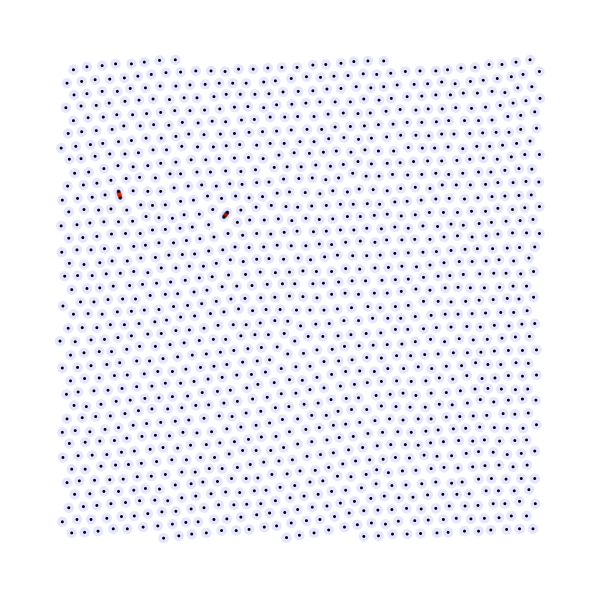
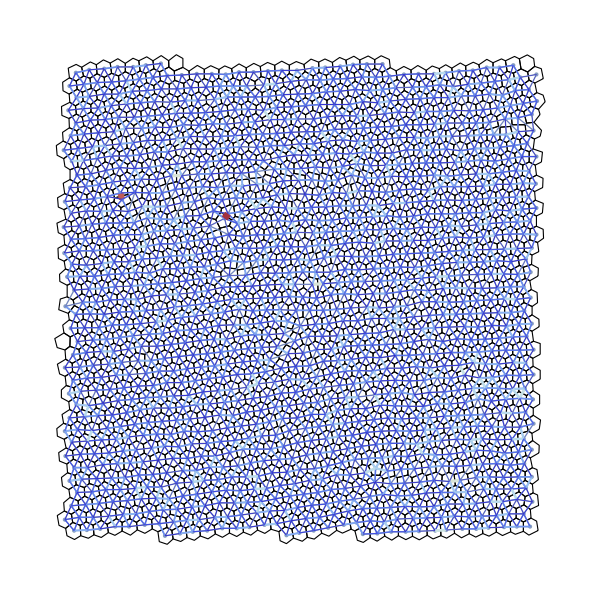

```mathematica
contactPlotsHexagonal
```